=== 1.1 解析解求解 ===

通解为：{{x[t]→ⅇ^(1/2 (-gamma/m-(√(gamma^2-4 k m))/m) t) C[1]+ⅇ^(1/2 (-gamma/m+(√(gamma^2-4 k m))/m) t) C[2]}}

=== 1.2 三种情况特解 (x(0)=1, x'(0)=0) ===

欠阻尼 x(t) = 1. ⅇ^(-0.1 t) (1. Cos[0.994987 t]+0.100504 Sin[0.994987 t])

临界阻尼 x(t) = ⅇ^-t (1+t)

过阻尼 x(t) = 1/6 (3 ⅇ^((-2-√3) t)-2 √3 ⅇ^((-2-√3) t)+3 ⅇ^((-2+√3) t)+2 √3 ⅇ^((-2+√3) t))

=== 1.3 可视化比较 ===

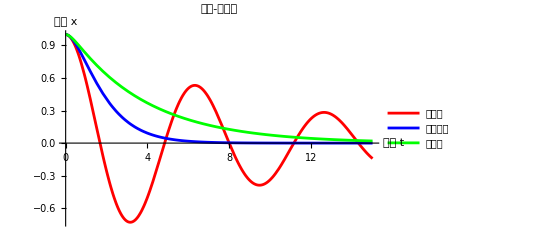

正在绘制相图...（现在应该不会报错了）

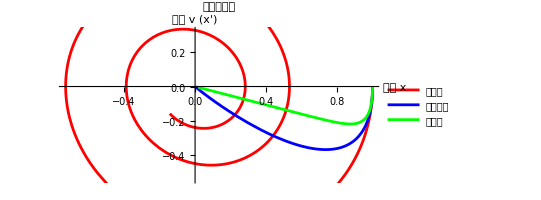

```mathematica
(* =================================================*)(*任务一：阻尼振动的完整分析（修正）*)(* =================================================*)Clear["Global`*"] (*变量都清空，防止干扰*)

(*1. 定义方程*)
(*这里的 x[t] 别忘了加[t]*)
eqn=m*x''[t]+gamma*x'[t]+k*x[t]==0;

(*-------1.1 解析解-------*)
Print["=== 1.1 解析解求解 ==="];
solGeneral=DSolve[eqn,x[t],t];
Print["通解为：",solGeneral];

(*-------1.2 求特解-------*)
Print["\n=== 1.2 三种情况特解 (x(0)=1, x'(0)=0) ==="];

mVal=1;kVal=1;
ic={x[0]==1,x'[0]==0};

(*辅助函数：帮忙代入参数解方程*)
solveCase[gVal_]:=Module[{currentEqn},currentEqn=eqn/. {m->mVal,k->kVal,gamma->gVal};
(*DSolveValue 直接给表达式，不用再提取规则了*)DSolveValue[{currentEqn,ic},x[t],t]];

(*分别算出三个位移表达式*)
solUnder=solveCase[0.2]; (*欠阻尼*)
solCritical=solveCase[2]; (*临界阻尼*)
solOver=solveCase[4];    (*过阻尼*)

Print["欠阻尼 x(t) = ",solUnder];
Print["临界阻尼 x(t) = ",solCritical];
Print["过阻尼 x(t) = ",solOver];

(*-------1.3 可视化比较（重点！这里修正了报错）-------*)
Print["\n=== 1.3 可视化比较 ==="];

(*画位移-时间图*)
plotXt=Plot[{solUnder,solCritical,solOver},{t,0,15},PlotRange->All,PlotStyle->{Red,Blue,Green},PlotLegends->{"欠阻尼","临界阻尼","过阻尼"},AxesLabel->{"时间 t","位移 x"},PlotLabel->"位移-时间图"];
Print[plotXt];

(*画相图 (x,v)*)
(*!!!修正笔记：之前直接在 ParametricPlot 里写 D[sol,t] 报错了!!!*)
(*报错说 D 不是有效变量，因为画图时 t 先变成了数字。*)
(*所以我必须先在外面把速度 v 算出来，变成表达式，再放进去画。*)

vUnder=D[solUnder,t];     (*先求导，算出速度表达式*)
vCritical=D[solCritical,t];
vOver=D[solOver,t];

Print["正在绘制相图...（现在应该不会报错了）"];

plotPhase=ParametricPlot[{{solUnder,vUnder},{solCritical,vCritical},{solOver,vOver}},{t,0,15},PlotStyle->{Red,Blue,Green},PlotLegends->{"欠阻尼","临界阻尼","过阻尼"},AxesLabel->{"位移 x","速度 v (x')"},PlotLabel->"相空间轨迹"];

Print[plotPhase];
```